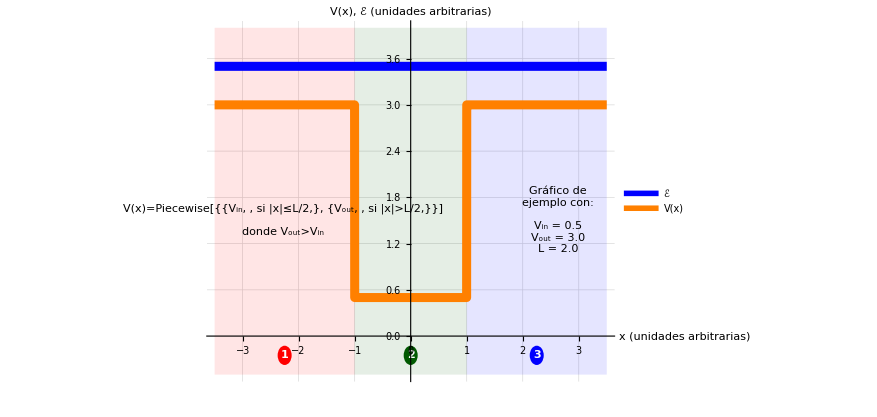
Pozo finito de potencial, caso (a).

Este archivo muestra cómo resolver la ecuación de Schrödinger independiente del tiempo (ESIT) para un pozo finito de potencial cuando la energía de la partícula supera al potencial en todo punto.

-Graphics-

Para cada región indicada en la figura tendremos una ESIT de la forma 

	-ℏ^2/(2m)(ⅆ^2 ψ_j)/(ⅆ x^2)+V_j ψ_j= ℰ ψ_j, 	donde 	j=1,2,3, 	V_1=V_3=V_out 	y	V_2=V_in.

Estas ecuaciones son equivalentes a 	ψ''_j(x)+k_j^2 ψ_j(x)=0,	donde	k_1 | = | √((2m)/ℏ^2(ℰ-V_out)) | = | k_out,
k_2 | = | √((2m)/ℏ^2(ℰ-V_in)) | = | k_in,
k_3 | = | √((2m)/ℏ^2(ℰ-V_out)) | = | k_out. 

Las soluciones para cada región serán de la forma 	ψ_j(x)=A_j ⅇ^(ⅈ k_j x) + B_j ⅇ^(-ⅈ k_j x),	donde los coeficientes A_j y B_j son incógnitas a determinar. 

Para simplificar la descripción, hay algunos parámetros auxiliares que usaremos en ocasiones: 

	ΔV | = | V_out-V_in | : | "profundidad" del pozo.    										
Δℰ | = | ℰ-V_in | : | indica cuánto sobresale la energía ℰ por encima del fondo del pozo.           	
η | = | Δℰ/ΔV | : | ubicación de la energía ℰ relativa a la profundidad del pozo.     			
  |   |   |   | Por ejemplo, η=1/2 indica que ℰ  está exactamente a la mitad entre V_in y V_out.    
λ_dB | = | √((2 π^2 ℏ^2)/(m Δℰ)) | : | longitud de onda de de Broglie de la partícula, tomando Δℰ como referencia.
  |   |   |   | •  Imagine que la energía cinética (p^2/2m) de la partícula fuese Δℰ.
  |   |   |   | • Entonces, p=√(2m Δℰ).            							
  |   |   |   | • La hipótesis de de Broglie dice que p=ℏk, donde k=2π/λ_dB.         
  |   |   |   | • Despejando, se obtiene que λ_dB=√((2 π^2 ℏ^2)/(m Δℰ)).    				
Λ | = | L/λ_dB | : | ancho del pozo, pero expresado en múltiplos de λ_dB.       				   	

Con estas sustituciones, podemos escribir también que	k_in | = | √((2m)/ℏ^2 Δℰ) | = | √((2m ΔV)/ℏ^2)√η | ,
k_out | = | √((2m)/ℏ^2(Δℰ-ΔV)) | = | √((2m ΔV)/ℏ^2)√(η-1) | ,
Λ | = | L √(m/(2 π^2 ℏ^2)Δℰ) | = | L/(2π)√((2m ΔV)/ℏ^2)√η | .

Condiciones de continuidad.

Se impone que la función de onda sea continua para que la probabilidad de encontrar a la partícula en una zona no tenga vacíos físicamente inadmisibles. 

Dado que el potencial V(x) es finito en todo su dominio, la derivada de la función de onda también es continua. 

Los puntos “problemáticos” son x=±L/2, que es donde el potencial exhibe discontinuidades y, a causa de ello, es también donde separamos la función de onda en tramos. Impondremos las condiciones de continuidad en esos puntos x=±L/2: 

	ψ_1^(-L/2) | = | ψ_2^(-L/2)  | 		⇒		 | A_1 ⅇ^(-1/2 ⅈ L k_out)+B_1 ⅇ^(1/2 ⅈ L k_out) | = | A_2 ⅇ^(-1/2 ⅈ L k_in)+B_2 ⅇ^(1/2 ⅈ L k_in)
ψ_1^′(-L/2) | = | ψ_2^′(-L/2)  | 		⇒		 | ⅈ A_1 k_out ⅇ^(-1/2 ⅈ L k_out)-ⅈ B_1 k_out ⅇ^(1/2 ⅈ L k_out) | = | ⅈ A_2 k_in ⅇ^(-1/2 ⅈ L k_in)-ⅈ B_2 k_in ⅇ^(1/2 ⅈ L k_in)
ψ_2^(+L/2) | = | ψ_3^(+L/2)  | 		⇒		 | A_2 ⅇ^(1/2 ⅈ L k_in)+B_2 ⅇ^(-1/2 ⅈ L k_in) | = | A_3 ⅇ^(1/2 ⅈ L k_out)+B_3 ⅇ^(-1/2 ⅈ L k_out)
ψ_2^′(+L/2) | = | ψ_3^′(+L/2)  | 		⇒		 | ⅈ A_2 k_in ⅇ^(1/2 ⅈ L k_in)-ⅈ B_2 k_in ⅇ^(-1/2 ⅈ L k_in) | = | ⅈ A_3 k_out ⅇ^(1/2 ⅈ L k_out)-ⅈ B_3 k_out ⅇ^(-1/2 ⅈ L k_out)

Así, estas cuatro ecuaciones forman un sistema de ecuaciones lineales para los coeficientes A_1,B_1,A_2,B_2,A_3,B_3. Otras ecuaciones y/o condiciones adicionales se verán caso a caso.

Caso (a): ℰ>V_out>V_in

En las tres regiones tendremos soluciones oscilatorias, pues todos los k_j son reales y positivos. Así que no tenemos confinamiento en este régimen. 
Debido a ello, podemos suponer que la partícula viene desde lejos como, por ejemplo, desde x=-∞. Entonces, A_1 será el coeficiente de referencia ya que indica la amplitud de la onda incidente. 

La onda no tiene con qué reflejarse en la Región 3, así que es de esperar que B_3=0. 
Con ello, las condiciones de continuidad constuyen un sistema no homogéneo de 4 ecuaciones lineales para las incógnitas B_1,A_2,B_2 y A_3, que serán expresadas en función de A_1: 

	-A_2 ⅇ^(-1/2 ⅈ L k_in) - B_2 ⅇ^(1/2 ⅈ L k_in) + B_1 ⅇ^(1/2 ⅈ L k_out) | = | A_1 ⅇ^(-1/2 ⅈ L k_out)
-ⅈ A_2 k_in ⅇ^(-1/2 ⅈ L k_in) + ⅈ B_2 k_in ⅇ^(1/2 ⅈ L k_in) - ⅈ B_1 k_out ⅇ^(1/2 ⅈ L k_out) | = | ⅈ A_1 k_out ⅇ^(-1/2 ⅈ L k_out)
A_2 ⅇ^(1/2 ⅈ L k_in) - A_3 ⅇ^(1/2 ⅈ L k_out) + B_2 ⅇ^(-1/2 ⅈ L k_in) | = | 0
ⅈ A_2 k_in ⅇ^(1/2 ⅈ L k_in) - ⅈ A_3 k_out ⅇ^(1/2 ⅈ L k_out) - ⅈ B_2 k_in ⅇ^(-1/2 ⅈ L k_in) | = | 0

Este sistema se puede representar matricialmente como  	M·v⃗=b⃗,	 donde:

  	• M es la matriz de coeficientes, M = (ⅇ^(1/2 ⅈ L k_out) | -ⅇ^(-1/2 ⅈ L k_in) | -ⅇ^(1/2 ⅈ L k_in) | 0
-ⅈ k_out ⅇ^(1/2 ⅈ L k_out) | -ⅈ k_in ⅇ^(-1/2 ⅈ L k_in) | ⅈ k_in ⅇ^(1/2 ⅈ L k_in) | 0
0 | ⅇ^(1/2 ⅈ L k_in) | ⅇ^(-1/2 ⅈ L k_in) | -ⅇ^(1/2 ⅈ L k_out)
0 | ⅈ k_in ⅇ^(1/2 ⅈ L k_in) | -ⅈ k_in ⅇ^(-1/2 ⅈ L k_in) | -ⅈ k_out ⅇ^(1/2 ⅈ L k_out)).
 	• v⃗ es el vector que contiene a las incógnitas, v⃗=(B_1
A_2
B_2
A_3) . 
 	• b⃗ es el término inhomogéneo del sistema y contiene a A_1,  b⃗=-A_1(ⅇ^(-1/2 ⅈ L k_out)
ⅈ k_out ⅇ^(-1/2 ⅈ L k_out)
0
0).

Siendo un sistema inhomogéneo, al despejar los coeficientes se obtendrá una solución no trivial (no serán solo ceros).

Coeficientes de reflexión y transmisión.

Si vemos al pozo de potencial como una “caja negra”, nuestro mayor interés estará en qué es lo que emerge de él cuando enviamos algo. Así suelen tratarse los problemas de scattering. 

En este contexto, se envió una onda desde x=-∞ hacia el pozo. Ahí puede ocurrir que una parte de esa onda se devuelva hacia la izquierda (reflexión) y que otra parte emerja hacia la derecha (transmisión). Las amplitudes de reflexión (𝓇) y transmisión (𝓉) contienen información de con cuánta probabilidad ocurrirá cada opción y si la onda gana alguna fase en ellas. 

	𝓇=B_1/A_1 	y 	𝓉=A_3/A_1.

En este cálculo se muestran estos coeficientes bajo la suposición de que la onda incidente viene desde la izquierda. 
Si se hubiera supuesto que la onda viene desde la derecha, se debe calcular 𝓇 y 𝓉 de acuerdo con ese convenio. 

 	• Suponga que 𝓇_± y 𝓉_± fuesen las amplitudes de reflexión y transmisión para una onda que va desde ∓∞ hacia ±∞. 
 		◦ El signo en el subíndice indica la dirección de propagación de la onda incidente, no su procedencia. 
 		◦ Los 𝓇 y 𝓉 de más arriba serían como estos 𝓇_+ y 𝓉_+, respectivamente. 
 	• Generalmente ocurrirá que 	𝓇_+≠𝓇_- 	y 	𝓉_+≠𝓉_-.
 	• No obstante, potenciales simétricos como el que estamos viendo aquí sí exhiben igualdad.
	
Luego, las probabilidades de que la partícula termine siendo reflejada o transmitida se calculan como solemos hacerlo en Mecánica Cuántica: módulo al cuadrado de las amplitudes.

	R=|𝓇|^2, 	y 	T=|𝓉|^2. 	


* Para ver los gráficos interactivos, ejecute la siguiente celda y vaya al final del archivo.

```mathematica
Remove["Global`*"];
$Assumptions=And@@Thread[{Subscript[k, in],Subscript[k, out],Subscript[Κ, P],Subscript[γ, in],Subscript[γ, out],L,ℒ,Λ,Subscript[λ, P],Subscript[λ, dB],m,ℏ,ℰ,η,Subscript[V, in],Subscript[V, out],ΔV,Δ𝒱,𝒜^◦,𝓂,𝓈,ℯ𝒱}>0]&&Δℰ>0&&η≥1;

(* Funciones de onda posibles. *)
Subscript[ψ, j_][x_]:=Subscript[A, j] ⅇ^(ⅈ Subscript[κ, j] x)+Subscript[B, j] ⅇ^(-ⅈ Subscript[κ, j] x);


(* Reducción de parámetros. *)
(* ΔV = Subscript[V, out] - Subscript[V, in], "profundidad" del pozo. *)
Reduccion={
	Subscript[k, in]->√((2m)/ℏ^2(ℰ-Subscript[V, in])),
	Subscript[k, out]->√((2m)/ℏ^2(ℰ-Subscript[V, out])),
	Subscript[γ, in]->√((2m)/ℏ^2(Subscript[V, in]-ℰ)),
	Subscript[γ, out]->√((2m)/ℏ^2(Subscript[V, out]-ℰ)),
	ℰ->Δℰ+Subscript[V, in],
	Subscript[V, out]->ΔV+Subscript[V, in],
	Δℰ->η ΔV,
	Subscript[λ, dB]->√((2 π^2 ℏ^2)/(m Δℰ)),
	L->Λ Subscript[λ, dB]		
};


(*"
Para gráficos, consideremos un electrón en un pozo que tiene unos cuantos årmströng de ancho y unos cuantos electronvolts de profundidad. Podemos ir cambiando L y ΔV.
"*)
Numeros={
		Subscript[k, in]->√((2m)/ℏ^2(ℰ-Subscript[V, in])),
		Subscript[k, out]->√((2m)/ℏ^2(ℰ-Subscript[V, out])),
		Subscript[γ, in]->√((2m)/ℏ^2(Subscript[V, in]-ℰ)),
		Subscript[γ, out]->√((2m)/ℏ^2(Subscript[V, out]-ℰ)),
		Subscript[λ, dB]->√((2 π^2 ℏ^2)/(m Δℰ)),
		ℰ->Δℰ+Subscript[V, in],
		Subscript[V, out]->ΔV+Subscript[V, in],
		Δℰ->η ΔV,
		c->299792458 𝓂/𝓈,
		ℏ->6.62607015/(2π)×10^-34 𝒥 𝓈,
		𝒥->ℯ𝒱/(1.60217663×10^-19),
		m->0.511 ×10^6 ℯ𝒱/c^2,
		𝓂->𝒜^◦/10^-10,
		L->ℒ 𝒜^◦,                                       (* ℒ: Ancho del pozo, pero medido en årmströngs. *)
		ΔV->Δ𝒱 ℯ𝒱,		             (* Δ𝒱: profundidad del pozo, pero medido en electronvolts. *)
		σ->5                                       (* σ: ancho del paquete de onda, en årmströngs. *)
};

(* Funciones solo para ayudar en la presentación de resultados. *)
TsT[args__]:=TraditionalForm[StringRiffle[ToString[#,TraditionalForm]&/@{args}]]

(* Condiciones de continuidad. *)
Continuidad={
			Subscript[ψ, 1][-L/2]==Subscript[ψ, 2][-L/2],
			Subscript[ψ, 1]'[-L/2]==Subscript[ψ, 2]'[-L/2],
			Subscript[ψ, 2][L/2]==Subscript[ψ, 3][L/2],
			Subscript[ψ, 2]'[L/2]==Subscript[ψ, 3]'[L/2]
			};


SubsA={Subscript[κ, 1]->Subscript[k, out],Subscript[κ, 2]->Subscript[k, in],Subscript[κ, 3]->Subscript[k, out],Subscript[B, 3]->0};
Subscript[Eqs, a]=Continuidad//.SubsA;
Subscript[v, a]={Subscript[B, 1],Subscript[A, 2],Subscript[B, 2],Subscript[A, 3]};

(* Podemos expresar el sistema de ecuaciones como M·v⃗=b⃗, donde: *)
{Subscript[b, a],Subscript[M, a]}=Normal[CoefficientArrays[Subscript[Eqs, a],Subscript[v, a]]];
Subscript[b, a]=-Subscript[b, a];             (* CoefficientArrays construye como Subscript[M, a].Subscript[v, a]+Subscript[b, a]=0. Nosotros usamos Subscript[M, a].Subscript[v, a]=Subscript[b, a]. *)

(* El sistema es inhomogéneo y se puede resolver sin caer en la solución trivial. *)
Subscript[S, a]=Flatten[FullSimplify[Solve[Subscript[Eqs, a],Subscript[v, a]]]];


TsT["Caso (a): ℰ>V_out>V_in\nSistema matricial M·v⃗ = b⃗\n",
	Subscript[M, a]·{Subscript[v, a]}ᵀ=={Subscript[b, a]}ᵀ,"\n\nSoluciones:\n",Flatten["\n"Subscript[S, a]]]

(* Nos interesan los coeficientes de reflexión y transmisión. *)
𝓇𝓉=FullSimplify[{Subscript[B, 1]/Subscript[A, 1],Subscript[A, 3]/Subscript[A, 1]}//. Subscript[S, a]];
RT=FullSimplify[𝓇𝓉* * 𝓇𝓉];
TsT["Cell["𝓇 = ",ExpressionUUID->"fe270ac2-eb05-44f4-95dd-5037e35ba4ad"]",𝓇𝓉⟦1⟧,"\n","Cell["𝓉 =",ExpressionUUID->"1b4065de-578b-4d5d-9204-25c7dd547acf"]",𝓇𝓉⟦2⟧,"\n","R = |𝓇|^2 = ",RT⟦1⟧,"\n","T = |𝓉|^2 = ",RT⟦2⟧]


(*" 
Grafiquemos estos coeficientes en función de la energía y la longitud, pero usando los parámetros reducidos. Es decir, energía como múltiplo de la profundidad del pozo y ancho del pozo como múltiplos de la longitud de onda de de Broglie. 
"*)
ηmin=1.00;
ηmax=5.0;
Λmin=0.01;
Λmax=6.0;
{dbR[η_,Λ_],dbT[η_,Λ_]}=FullSimplify[RT//.Reduccion];
TsT["Si Λ = L/λ_dB, entonces Cell["R = ",ExpressionUUID->"f0b0cec2-2bd1-496b-a14b-1b74cf3b6565"]",dbR[η,Λ],"\t y \t","Cell["T = ",ExpressionUUID->"d056fdf5-c9a6-4a89-8d9a-e73ae8c9f4a5"]",dbT[η,Λ],"."]
Manipulate[
		Plot[{dbR[η,Λ],dbT[η,Λ]},
			{Λ,Λmin,Λmax},
			PlotPoints->Ceiling[30(Λmax-Λmin)],
			PlotLegends->{"R","T"},
			AxesLabel->{"Λ = L/λ_dB","R, T"},
			PlotLabel->("Coeficientes de reflexión y transmisión\n"
						<>"Δℰ = "<>ToString[η]<>" ΔV"),
			GridLines->Automatic],
		{{η,1.02},ηmin,ηmax,(ηmax-ηmin)/100.},
		LabelStyle->Large,
		ControlPlacement->Top,
		SynchronousUpdating->False]


(*"
Más ejemplos gráficos, con números variados. 
Longitudes en amstrongs, energías en electronvolts. 
"*)
ℒmin=1.;
ℒmax=30.;
ΔVmin=1.;
ΔVmax=20.;
{B1[η_,ℒ_,Δ𝒱_],
A2[η_,ℒ_,Δ𝒱_],
B2[η_,ℒ_,Δ𝒱_],
A3[η_,ℒ_,Δ𝒱_]}=N[FullSimplify[{Subscript[B, 1],Subscript[A, 2],Subscript[B, 2],Subscript[A, 3]}//. Subscript[S, a]//.Numeros//.{Subscript[A, 1]->1},η≥1]];
numKin[η_,Δ𝒱_]=N[FullSimplify[Subscript[k, in] × 𝒜^◦//.Numeros]];
numKout[η_,Δ𝒱_]=N[FullSimplify[Subscript[k, out]× 𝒜^◦//.Numeros]];
A1=0.05ΔVmax ηmax;
KinMax=numKin[ηmax,ΔVmax];
dxmin=(2π)/(16KinMax);

colores=ColorData[97]/@Range[6];
leyenda=LineLegend[colores,
				{"Incidente desde 1",
				"Reflejado en frontera 1|2",
				"Transmitido 1→2",
				"Reflejado en frontera 2|3",
				"Transmitido 2→3",
				"Potencial"},
				LabelStyle->Larger];
Manipulate[
		kout=numKout[η,Δ𝒱]; 
		kin=numKin[η,Δ𝒱];
		B1n=B1[η,ℒ,Δ𝒱];
		A2n=A2[η,ℒ,Δ𝒱];
		B2n=B2[η,ℒ,Δ𝒱];
		A3n=A3[η,ℒ,Δ𝒱];
		h0=η Δ𝒱;
		LdB=ℒ/(2π/kin);
		
		npin=Ceiling[ℒ/dxmin];
		npout=Ceiling[(ℒmax-ℒ/2)/dxmin];
		𝓍1=Subdivide[-ℒmax,-ℒ/2,npout];
		𝓍2=Subdivide[-ℒ/2,ℒ/2,npin];
		𝓍3=Subdivide[ℒ/2,ℒmax,npout];

		Onda1d=h0+A1 Re[Exp[+ ⅈ kout 𝓍1]];
		Onda1i=h0+A1 Re[Exp[- ⅈ kout 𝓍1]×B1n];
		Onda2d=h0+A1 Re[Exp[+ ⅈ kin 𝓍2  ]×A2n];
		Onda2i=h0+A1 Re[Exp[- ⅈ kin 𝓍2  ]×B2n];
		Onda3d=h0+A1 Re[Exp[+ ⅈ kout 𝓍3]×A3n];
		Vx={{-ℒmax,Δ𝒱},{-ℒ/2,Δ𝒱},{-ℒ/2,0},{ℒ/2,0},{ℒ/2,Δ𝒱},{ℒmax,Δ𝒱}};

		ymaxW=(ΔVmax ηmax+3η Δ𝒱)/4+A1;
		PlotW=ListLinePlot[
					{{𝓍1,Onda1d}ᵀ,
					{𝓍1,Onda1i}ᵀ,
					{𝓍2,Onda2d}ᵀ,
					{𝓍2,Onda2i}ᵀ,
					{𝓍3,Onda3d}ᵀ,
					Vx},
					PlotStyle->colores,
					PlotLabel->("Δℰ = "<>ToString[η]<>" ΔV,\t"<>
							"ΔV = "<>ToString[Δ𝒱]<>" eV,\r"<>
							"L = "<>ToString[ℒ]<>" Å \t (o "<>ToString[LdB]<>"λ_dB),\r\r"<>
							"R = "<>ToString[Abs[B1n]^2]<>",\t"<>
							"T = "<>ToString[Abs[A3n]^2]<>"."),
					GridLines->{{-ℒ/2,ℒ/2},{}},
					PlotRange->{{-1,1}ℒmax,{-0.01ΔVmax,ymaxW}},
					FrameLabel->{"x, en Å","V(x), ψ(x)"},
					Frame->True];
		Legended[PlotW,Placed[leyenda,Right]],
		{{η,(ηmax+ηmin)/2.0},ηmin,ηmax,((ηmax-ηmin)/100.0)},
		{{ℒ,(ℒmax+ℒmin)/2.0},ℒmin,ℒmax,((ℒmax-ℒmin)/100.0)},
		{{Δ𝒱,(ΔVmax+ΔVmin)/2.0},ΔVmin,ΔVmax,((ΔVmax-ΔVmin)/100.0)},
		LabelStyle->Larger,
		ControlPlacement->Top,
		SynchronousUpdating->False]
```

Caso (a): ℰ>V_out>V_in
Sistema matricial M·v⃗ = b⃗
 (ⅇ^(1/2 ⅈ L k_out) | -ⅇ^(-1/2 ⅈ L k_in) | -ⅇ^(1/2 ⅈ L k_in) | 0
-ⅈ k_out ⅇ^(1/2 ⅈ L k_out) | -ⅈ k_in ⅇ^(-1/2 ⅈ L k_in) | ⅈ k_in ⅇ^(1/2 ⅈ L k_in) | 0
0 | ⅇ^(1/2 ⅈ L k_in) | ⅇ^(-1/2 ⅈ L k_in) | -ⅇ^(1/2 ⅈ L k_out)
0 | ⅈ k_in ⅇ^(1/2 ⅈ L k_in) | -ⅈ k_in ⅇ^(-1/2 ⅈ L k_in) | -ⅈ k_out ⅇ^(1/2 ⅈ L k_out))·(B_1
A_2
B_2
A_3)==(A_1 (-ⅇ^(-1/2 ⅈ L k_out))
-ⅈ A_1 k_out ⅇ^(-1/2 ⅈ L k_out)
0
0) 

Soluciones:
 {
 (B_1→(A_1 (-1+ⅇ^(2 ⅈ L k_in)) (k_out^2-k_in^2) ⅇ^(-ⅈ L k_out))/(-(k_in+k_out)^2+ⅇ^(2 ⅈ L k_in) (k_in-k_out)^2)),
 (A_2→-(2 A_1 k_out (k_in+k_out) ⅇ^(1/2 ⅈ L (k_in-k_out)))/(-(k_in+k_out)^2+ⅇ^(2 ⅈ L k_in) (k_in-k_out)^2)),
 (B_2→-(2 A_1 k_out (k_in-k_out) ⅇ^(1/2 ⅈ L (3 k_in-k_out)))/(-(k_in+k_out)^2+ⅇ^(2 ⅈ L k_in) (k_in-k_out)^2)),
 (A_3→-(4 A_1 k_in k_out ⅇ^(ⅈ L (k_in-k_out)))/(-(k_in+k_out)^2+ⅇ^(2 ⅈ L k_in) (k_in-k_out)^2))}

Cell["𝓇 = "] ((-1+ⅇ^(2 ⅈ L k_in)) (k_out^2-k_in^2) ⅇ^(-ⅈ L k_out))/(-(k_in+k_out)^2+ⅇ^(2 ⅈ L k_in) (k_in-k_out)^2) 
 Cell["𝓉 ="] -(4 k_in k_out ⅇ^(ⅈ L (k_in-k_out)))/(-(k_in+k_out)^2+ⅇ^(2 ⅈ L k_in) (k_in-k_out)^2) 
 R = |𝓇|^2 =  (2 (k_in^2-k_out^2)^2 sin^2(L k_in))/(-(k_in^2-k_out^2)^2 cos(2 L k_in)+6 k_in^2 k_out^2+k_in^4+k_out^4) 
 T = |𝓉|^2 =  (8 k_in^2 k_out^2)/(-(k_in^2-k_out^2)^2 cos(2 L k_in)+6 k_in^2 k_out^2+k_in^4+k_out^4)

Si Λ = L/λ_dB, entonces Cell["R = "] (2 sin^2(2 π Λ))/(8 (η-1) η-cos(4 π Λ)+1) 	 y 	 Cell["T = "] (8 (η-1) η)/(8 (η-1) η-cos(4 π Λ)+1) .

```mathematica
FullSimplify[(Thread[Subscript[M, a].Subscript[v, a]==-Subscript[b, a]])/Subscript[Eqs, a]]
```

{(ⅇ^(1/2 ⅈ L k_out) B_1==ⅇ^(-1/2 ⅈ L k_out) A_1+ⅇ^(-1/2 ⅈ L k_in) (A_2+ⅇ^(ⅈ L k_in) B_2))/(ⅇ^(-1/2 ⅈ L k_out) (A_1+ⅇ^(ⅈ L k_out) B_1)==ⅇ^(-1/2 ⅈ L k_in) (A_2+ⅇ^(ⅈ L k_in) B_2)),(ⅇ^(1/2 ⅈ L k_in) (ⅇ^(1/2 ⅈ L (k_in+k_out)) B_2 k_in-(A_1+ⅇ^(ⅈ L k_out) B_1) k_out)==ⅇ^(1/2 ⅈ L k_out) A_2 k_in)/(ⅇ^(1/2 ⅈ L k_out) A_2 k_in==ⅇ^(1/2 ⅈ L k_in) (ⅇ^(1/2 ⅈ L (k_in+k_out)) B_2 k_in+(A_1-ⅇ^(ⅈ L k_out) B_1) k_out)),1,1}

```mathematica
Subscript[Eqs, a]
```

{ⅇ^(-1/2 ⅈ L k_out) A_1+ⅇ^(1/2 ⅈ L k_out) B_1==ⅇ^(-1/2 ⅈ L k_in) A_2+ⅇ^(1/2 ⅈ L k_in) B_2,ⅈ ⅇ^(-1/2 ⅈ L k_out) A_1 k_out-ⅈ ⅇ^(1/2 ⅈ L k_out) B_1 k_out==ⅈ ⅇ^(-1/2 ⅈ L k_in) A_2 k_in-ⅈ ⅇ^(1/2 ⅈ L k_in) B_2 k_in,ⅇ^(1/2 ⅈ L k_in) A_2+ⅇ^(-1/2 ⅈ L k_in) B_2==ⅇ^(1/2 ⅈ L k_out) A_3,ⅈ ⅇ^(1/2 ⅈ L k_in) A_2 k_in-ⅈ ⅇ^(-1/2 ⅈ L k_in) B_2 k_in==ⅈ ⅇ^(1/2 ⅈ L k_out) A_3 k_out}